# -Graphics-

# Wolfram 语言编程：概念到应用

## 模式和字符串模式

-Graphics-

## 学习对象

### 模式

基本模式对象

名称与 Head

PatternTest 与 Condition

特殊模式，例如：Repeated、Except 等

### 字符串模式

基本字符串模式

特殊字符串模式，例如：DigitCharacter、StartOfString 等

正则表达式

用法范例

# 模式

## 基本模式对象

替代平方的模式（不是立方）：

```mathematica
{ a^2, a^3,b^2,b^3,c^2,c^3 }/. _^2 -> 100
```

{100,a^3,100,b^3,100,c^3}

Wolfram 语言™中良好编程的重要组成部分是有效使用模式匹配. 模式定义为一类包含模式对象的表达式，这些对象可以表示可能的表达式集.

#### 一个表达式

Blank (_) 模式对象可以表示任何 Wolfram 语言表达式：

```mathematica
Clear[f,g]
```

```mathematica
{1,f[],f[a],f[a,b],g[e1,e2]}/.f[_]-> xxx
```

{1,f[],xxx,f[a,b],g[e1,e2]}

#### 一个或多个表达式

BlankSequence (__) 模式对象表示一个或多个 Wolfram 语言表达式的任意序列：

```mathematica
{1,f[],f[a],f[a,b],g[e1,e2]}/.f[__]-> xxx
```

{1,f[],xxx,xxx,g[e1,e2]}

#### 零个或多个表达式

BlankNullSequence (___) 模式对象表示零个或多个 Wolfram 语言表达式的任意序列：

```mathematica
{1,f[],f[a],f[a,b],g[e1,e2]}/.f[___]-> xxx
```

## 使用模式

模式匹配函数的一些范例：

```mathematica
ReplaceAll[{1,2,f1[10],f2[10],x,y,f1[20]},f1[_]->"Replaced"]
```

{1,2,Replaced,f2[10],x,y,Replaced}

```mathematica
{1,2,f1[10],f2[10],x,y,f1[20]}/.f1[_]->"Replaced"
```

{1,2,Replaced,f2[10],x,y,Replaced}

```mathematica
Cases[{1,2,f1[10],f2[10],x,y,f1[20]},f1[_]]
```

{f1[10],f1[20]}

```mathematica
Position[{1,2,f1[10],f2[10],x,y,f1[20]},f1[_]]
```

{{3},{7}}

```mathematica
Count[{1,2,f1[10],f2[10],x,y,f1[20]},f1[_]]
```

2

```mathematica
DeleteCases[{1,2,f1[10],f2[10],x,y,f1[20]},f1[_]]
```

{1,2,f2[10],x,y}

```mathematica
MemberQ[{1,2,f1[10],f2[10],x,y,f1[20]},f1[_]]
```

True

```mathematica
FreeQ[{1->k1,2->k2,f1[10]->k3,f2[10]->k4,x->k5,y->k6,f1[20]->k7},f1[_]]
```

False

```mathematica
MatchQ[f1[10],f1[_]]
```

True

```mathematica
ReplaceRepeated[{f[x],f[f[x]],f[f[f[x]]]} , f[x_]->x]
```

{x,x,x}

```mathematica
f[f[x]]
```

```mathematica
f[x]
```

```mathematica
x
```

```mathematica
Clear[x]
f1[x_]=x^2
f1[5]
```

x^2

25

```mathematica
f1[5.5]
```

30.25

```mathematica
f1[a]
```

a^2

```mathematica
Clear[x]
f1[x_]:=x^2
f1[5]
```

25

```mathematica
ClearAll[f1]
```

## MatchQ

MatchQ 可用于检验表达式是否匹配模式：

```mathematica
MatchQ[a,_]
```

True

```mathematica
MatchQ[4,_]
```

True

```mathematica
MatchQ[4.32,_]
```

True

```mathematica
MatchQ["myString",_]
```

True

```mathematica
MatchQ[RGBColor[1, 0, 0],_]
```

True

```mathematica
RGBColor[1,0,0]
```

RGBColor[1, 0, 0]

```mathematica
MatchQ[RGBColor[1, 0, 0],RGBColor[_]]
```

False

```mathematica
MatchQ[RGBColor[1, 0, 0],RGBColor[__]]
```

True

```mathematica
MatchQ[RGBColor[1, 0, 0],RGBColor[_,_,_]]
```

True

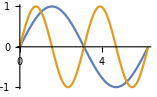
```mathematica
plt=-Graphics-;
MatchQ[plt,Graphics[__]]
```

True

```mathematica
plt//FullForm
```

Graphics[List[List[List[],List[],Annotation[List[RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[1.],Line[List[List[1.28228×10^-7,1.28228×10^-7],List[0.00192717,0.00192716],List[0.0038542,0.00385419],List[0.00770828,0.0077082],List[0.0154164,0.0154158],List[0.0308327,0.0308278],List[0.0616653,0.0616262],List[0.123331,0.123018],List[0.257035,0.254214],List[0.381879,0.372665],List[0.504274,0.483172],List[0.637043,0.594821],List[0.760951,0.68961],List[0.895233,0.780355],List[0.897293,0.781642],List[0.899353,0.782925],List[0.903473,0.785481],List[0.911713,0.790554],List[0.928192,0.800538],List[0.96115,0.819851],List[1.02707,0.855785],List[1.02899,0.856778],List[1.03091,0.857767],List[1.03475,0.859736],List[1.04244,0.863636],List[1.05781,0.871283],List[1.08855,0.885957],List[1.09047,0.886846],List[1.0924,0.887733],List[1.09624,0.889495],List[1.10393,0.892981],List[1.1193,0.899794],List[1.15004,0.91278],List[1.15212,0.913629],List[1.15421,0.914474],List[1.15837,0.916153],List[1.16671,0.919461],List[1.18338,0.925887],List[1.21671,0.937965],List[1.2188,0.938685],List[1.22088,0.939402],List[1.22505,0.940822],List[1.23338,0.943614],List[1.25005,0.949],List[1.28339,0.958981],List[1.28533,0.959531],List[1.28728,0.960077],List[1.29117,0.961158],List[1.29895,0.963276],List[1.31451,0.967338],List[1.31645,0.967829],List[1.3184,0.968316],List[1.32229,0.969281],List[1.33007,0.971165],List[1.34563,0.974757],List[1.34758,0.975189],List[1.34952,0.975618],List[1.35341,0.976465],List[1.36119,0.978113],List[1.37675,0.981232],List[1.3787,0.981606],List[1.38064,0.981975],List[1.38453,0.982703],List[1.39231,0.984114],List[1.40787,0.986757],List[1.40978,0.987065],List[1.41169,0.987369],List[1.4155,0.987966],List[1.42313,0.989117],List[1.42504,0.989396],List[1.42694,0.989671],List[1.43076,0.99021],List[1.43838,0.991246],List[1.44029,0.991496],List[1.4422,0.991742],List[1.44601,0.992224],List[1.45364,0.993145],List[1.46889,0.994812],List[1.4708,0.995004],List[1.47271,0.995193],List[1.47652,0.995559],List[1.48415,0.996248],List[1.48605,0.996412],List[1.48796,0.996571],List[1.49177,0.996879],List[1.4994,0.997452],List[1.50131,0.997587],List[1.50322,0.997717],List[1.50703,0.997968],List[1.50894,0.998087],List[1.51084,0.998203],List[1.51466,0.998425],List[1.51656,0.99853],List[1.51847,0.998631],List[1.52228,0.998824],List[1.52419,0.998914],List[1.5261,0.999001],List[1.52991,0.999164],List[1.53198,0.999247],List[1.53405,0.999325],List[1.53612,0.999399],List[1.53819,0.999468],List[1.54026,0.999534],List[1.54232,0.999595],List[1.54646,0.999704],List[1.54853,0.999752],List[1.5506,0.999796],List[1.55267,0.999836],List[1.55474,0.999871],List[1.55681,0.999902],List[1.55888,0.999929],List[1.56095,0.999951],List[1.56301,0.99997],List[1.56508,0.999984],List[1.56715,0.999993],List[1.56922,0.999999],List[1.57129,1.],List[1.57336,0.999997],List[1.57543,0.999989],List[1.5775,0.999978],List[1.57957,0.999962],List[1.58163,0.999941],List[1.5837,0.999917],List[1.58577,0.999888],List[1.58784,0.999855],List[1.58991,0.999817],List[1.59198,0.999776],List[1.59405,0.99973],List[1.59612,0.999679],List[1.59819,0.999625],List[1.60025,0.999566],List[1.60232,0.999503],List[1.60439,0.999436],List[1.60646,0.999364],List[1.60853,0.999288],List[1.61267,0.999123],List[1.61474,0.999035],List[1.61681,0.998942],List[1.62094,0.998743],List[1.62922,0.998294],List[1.63129,0.998171],List[1.63336,0.998044],List[1.6375,0.997776],List[1.64577,0.997191],List[1.64784,0.997034],List[1.64991,0.996872],List[1.65405,0.996537],List[1.66232,0.995814],List[1.66425,0.995636],List[1.66618,0.995454],List[1.67004,0.995079],List[1.67777,0.994284],List[1.6797,0.994076],List[1.68163,0.993864],List[1.68549,0.99343],List[1.69321,0.992517],List[1.69514,0.992279],List[1.69707,0.992038],List[1.70093,0.991544],List[1.70865,0.990513],List[1.7241,0.988272],List[1.72603,0.987976],List[1.72796,0.987675],List[1.73182,0.987064],List[1.73954,0.985796],List[1.75499,0.983085],List[1.78587,0.97696],List[1.78797,0.976511],List[1.79006,0.976058],List[1.79424,0.975139],List[1.80261,0.97325],List[1.81936,0.969268],List[1.85284,0.96049],List[1.85493,0.959905],List[1.85702,0.959316],List[1.86121,0.958126],List[1.86958,0.955696],List[1.88632,0.950635],List[1.9198,0.939714],List[1.92185,0.93901],List[1.92391,0.938301],List[1.92802,0.936873],List[1.93623,0.933968],List[1.95267,0.927969],List[1.98554,0.915221],List[2.05128,0.886774],List[2.05319,0.885887],List[2.05511,0.884996],List[2.05894,0.883206],List[2.0666,0.879586],List[2.08193,0.872191],List[2.11258,0.856789],List[2.17389,0.823584],List[2.17597,0.822404],List[2.17805,0.82122],List[2.1822,0.818841],List[2.19051,0.814042],List[2.20714,0.804275],List[2.24039,0.784076],List[2.30688,0.741103],List[2.43101,0.652275],List[2.56551,0.54474],List[2.69757,0.429578],List[2.82076,0.315355],List[2.95433,0.186171],List[3.07904,0.0625152],List[3.2013,-0.0596671],List[3.33393,-0.191151],List[3.4577,-0.310869],List[3.59185,-0.435193],List[3.72354,-0.549654],List[3.84638,-0.647871],List[3.97959,-0.743305],List[3.98153,-0.744603],List[3.98348,-0.745899],List[3.98736,-0.748481],List[3.99513,-0.753613],List[4.01068,-0.763738],List[4.04176,-0.783434],List[4.10394,-0.820535],List[4.10584,-0.821623],List[4.10775,-0.822707],List[4.11156,-0.824866],List[4.11918,-0.82915],List[4.13442,-0.837571],List[4.16489,-0.853829],List[4.1668,-0.854819],List[4.1687,-0.855806],List[4.17251,-0.85777],List[4.18013,-0.861662],List[4.19537,-0.869294],List[4.22584,-0.883952],List[4.22791,-0.884917],List[4.22997,-0.885877],List[4.23411,-0.887787],List[4.24238,-0.891562],List[4.25891,-0.898928],List[4.29198,-0.912921],List[4.29405,-0.913763],List[4.29611,-0.914601],List[4.30025,-0.916264],List[4.30851,-0.919545],List[4.32505,-0.925916],List[4.35812,-0.937899],List[4.36004,-0.938566],List[4.36197,-0.93923],List[4.36583,-0.940547],List[4.37354,-0.943139],List[4.38897,-0.948154],List[4.41982,-0.957507],List[4.42175,-0.958061],List[4.42368,-0.958612],List[4.42754,-0.959703],List[4.43525,-0.961842],List[4.45068,-0.965948],List[4.48153,-0.97347],List[4.48362,-0.973947],List[4.48571,-0.974419],List[4.48989,-0.97535],List[4.49825,-0.977161],List[4.51498,-0.980578],List[4.51707,-0.980986],List[4.51916,-0.981389],List[4.52334,-0.982183],List[4.5317,-0.98372],List[4.54843,-0.986588],List[4.55052,-0.986927],List[4.55261,-0.987262],List[4.55679,-0.987918],List[4.56515,-0.98918],List[4.56724,-0.989484],List[4.56933,-0.989784],List[4.57351,-0.990372],List[4.58187,-0.991495],List[4.58396,-0.991765],List[4.58605,-0.99203],List[4.59023,-0.992548],List[4.5986,-0.993533],List[4.61532,-0.995292],List[4.61727,-0.99548],List[4.61922,-0.995663],List[4.62313,-0.996019],List[4.63094,-0.996684],List[4.63289,-0.996841],List[4.63484,-0.996995],List[4.63874,-0.997289],List[4.64655,-0.997833],List[4.6485,-0.99796],List[4.65046,-0.998083],List[4.65436,-0.998317],List[4.65631,-0.998428],List[4.65826,-0.998536],List[4.66217,-0.998739],List[4.66412,-0.998835],List[4.66607,-0.998928],List[4.66998,-0.999101],List[4.67193,-0.999182],List[4.67388,-0.999259],List[4.67778,-0.999401],List[4.67974,-0.999467],List[4.68169,-0.999529],List[4.68364,-0.999587],List[4.68559,-0.999641],List[4.68754,-0.999691],List[4.6895,-0.999738],List[4.69145,-0.999781],List[4.6934,-0.99982],List[4.69535,-0.999855],List[4.6973,-0.999886],List[4.69926,-0.999914],List[4.70121,-0.999937],List[4.70316,-0.999957],List[4.70511,-0.999974],List[4.70706,-0.999986],List[4.70902,-0.999994],List[4.71097,-0.999999],List[4.71292,-1.],List[4.71487,-0.999997],List[4.71682,-0.99999],List[4.71878,-0.99998],List[4.72073,-0.999965],List[4.72268,-0.999947],List[4.72463,-0.999925],List[4.72658,-0.999899],List[4.72854,-0.99987],List[4.73049,-0.999836],List[4.73244,-0.999799],List[4.73439,-0.999758],List[4.73634,-0.999713],List[4.74025,-0.999612],List[4.74216,-0.999557],List[4.74408,-0.999498],List[4.7479,-0.999369],List[4.74982,-0.9993],List[4.75173,-0.999226],List[4.75556,-0.999068],List[4.75747,-0.998984],List[4.75939,-0.998896],List[4.76321,-0.998709],List[4.77087,-0.998291],List[4.77278,-0.998177],List[4.77469,-0.99806],List[4.77852,-0.997814],List[4.78618,-0.997279],List[4.78809,-0.997136],List[4.79,-0.996989],List[4.79383,-0.996685],List[4.80149,-0.996033],List[4.8034,-0.995861],List[4.80531,-0.995686],List[4.80914,-0.995323],List[4.8168,-0.994554],List[4.81871,-0.994353],List[4.82062,-0.994148],List[4.82445,-0.993727],List[4.83211,-0.992842],List[4.83402,-0.992612],List[4.83593,-0.992378],List[4.83976,-0.991899],List[4.84742,-0.990898],List[4.86273,-0.988721],List[4.8648,-0.988407],List[4.86688,-0.98809],List[4.87103,-0.987443],List[4.87933,-0.986097],List[4.89594,-0.983202],List[4.89802,-0.982821],List[4.90009,-0.982435],List[4.90424,-0.981652],List[4.91255,-0.980035],List[4.92915,-0.976598],List[4.93123,-0.97615],List[4.93331,-0.975697],List[4.93746,-0.974779],List[4.94576,-0.972892],List[4.96237,-0.968918],List[4.99558,-0.960169],List[4.99752,-0.959625],List[4.99945,-0.959079],List[5.00333,-0.957974],List[5.01108,-0.955723],List[5.02658,-0.951047],List[5.05758,-0.941012],List[5.05951,-0.940355],List[5.06145,-0.939694],List[5.06533,-0.938362],List[5.07308,-0.935655],List[5.08857,-0.930073],List[5.11957,-0.91824],List[5.12167,-0.917406],List[5.12377,-0.916569],List[5.12797,-0.914882],List[5.13637,-0.911459],List[5.15316,-0.904421],List[5.18676,-0.889582],List[5.25394,-0.85691],List[5.256,-0.855846],List[5.25806,-0.854778],List[5.26218,-0.852631],List[5.27043,-0.848294],List[5.28692,-0.839448],List[5.3199,-0.821072],List[5.38586,-0.781663],List[5.50892,-0.699195],List[5.64235,-0.597868],List[5.76692,-0.493638],List[5.88904,-0.38402],List[6.02154,-0.258675],List[6.14517,-0.137577],List[6.14733,-0.13544],List[6.14948,-0.133304],List[6.1538,-0.129028],List[6.16242,-0.120469],List[6.17967,-0.103326],List[6.21418,-0.0689526],List[6.21633,-0.0668011],List[6.21849,-0.0646493],List[6.2228,-0.0603447],List[6.23143,-0.0517324],List[6.24868,-0.0344969],List[6.25084,-0.0323416],List[6.25299,-0.0301862],List[6.25731,-0.0258749],List[6.26593,-0.0172511],List[6.26809,-0.0150949],List[6.27025,-0.0129386],List[6.27456,-0.00862592],List[6.27672,-0.00646951],List[6.27887,-0.00431306],List[6.28103,-0.0021566],List[6.28319,-1.28228×10^-7]]]],"Charting`Private`Tag$144428#1"],Annotation[List[RGBColor[0.880722,0.611041,0.142051],AbsoluteThickness[1.6],Opacity[1.],Line[List[List[1.28228×10^-7,2.56457×10^-7],List[0.00192717,0.00385432],List[0.0038542,0.00770833],List[0.00770828,0.0154159],List[0.0154164,0.030828],List[0.0308327,0.0616264],List[0.0616653,0.123018],List[0.123331,0.244167],List[0.257035,0.491725],List[0.258985,0.495118],List[0.260936,0.498504],List[0.264838,0.505253],List[0.27264,0.518658],List[0.288246,0.545086],List[0.319457,0.596324],List[0.321407,0.599451],List[0.323358,0.602569],List[0.327259,0.608778],List[0.335062,0.621084],List[0.350668,0.645239],List[0.381879,0.69164],List[0.383791,0.694397],List[0.385704,0.697145],List[0.389528,0.702609],List[0.397178,0.713413],List[0.412477,0.734517],List[0.443076,0.774644],List[0.444989,0.777057],List[0.446901,0.779459],List[0.450726,0.784229],List[0.458376,0.793629],List[0.473675,0.811871],List[0.504274,0.846058],List[0.506348,0.848263],List[0.508423,0.850453],List[0.512572,0.854789],List[0.52087,0.863284],List[0.537466,0.879558],List[0.53954,0.881524],List[0.541615,0.883476],List[0.545764,0.887333],List[0.554062,0.894863],List[0.570658,0.909182],List[0.572733,0.910902],List[0.574807,0.912606],List[0.578956,0.915967],List[0.587254,0.9225],List[0.60385,0.934802],List[0.605925,0.936267],List[0.607999,0.937717],List[0.612148,0.940567],List[0.620446,0.946074],List[0.637043,0.956303],List[0.638979,0.957428],List[0.640915,0.958539],List[0.644787,0.960717],List[0.652531,0.9649],List[0.654467,0.96591],List[0.656403,0.966905],List[0.660275,0.968852],List[0.66802,0.972571],List[0.669956,0.973464],List[0.671892,0.974343],List[0.675764,0.976057],List[0.683508,0.979309],List[0.685444,0.980085],List[0.68738,0.980846],List[0.691253,0.982326],List[0.698997,0.985107],List[0.700933,0.985765],List[0.702869,0.986409],List[0.706741,0.987652],List[0.714485,0.98996],List[0.716421,0.9905],List[0.718357,0.991025],List[0.72223,0.99203],List[0.729974,0.993863],List[0.73191,0.994283],List[0.733846,0.994689],List[0.737718,0.995457],List[0.739654,0.995818],List[0.74159,0.996164],List[0.745462,0.996812],List[0.747399,0.997113],List[0.749335,0.9974],List[0.751271,0.997672],List[0.753207,0.997928],List[0.755143,0.99817],List[0.757079,0.998396],List[0.760951,0.998805],List[0.763049,0.999001],List[0.765147,0.99918],List[0.767246,0.999341],List[0.769344,0.999485],List[0.771442,0.99961],List[0.77354,0.999719],List[0.775638,0.999809],List[0.777736,0.999883],List[0.779835,0.999938],List[0.781933,0.999976],List[0.784031,0.999996],List[0.786129,0.999999],List[0.788227,0.999984],List[0.790325,0.999951],List[0.792423,0.999901],List[0.794522,0.999834],List[0.79662,0.999748],List[0.798718,0.999645],List[0.800816,0.999525],List[0.802914,0.999386],List[0.805012,0.999231],List[0.807111,0.999057],List[0.809209,0.998866],List[0.811307,0.998658],List[0.813405,0.998432],List[0.815503,0.998188],List[0.817601,0.997927],List[0.8197,0.997648],List[0.821798,0.997351],List[0.823896,0.997037],List[0.828092,0.996357],List[0.83019,0.99599],List[0.832289,0.995606],List[0.836485,0.994785],List[0.838583,0.994348],List[0.840681,0.993894],List[0.844878,0.992933],List[0.846976,0.992426],List[0.849074,0.991902],List[0.85327,0.990801],List[0.861663,0.98839],List[0.863761,0.987744],List[0.865859,0.98708],List[0.870055,0.9857],List[0.878448,0.982733],List[0.880546,0.981948],List[0.882644,0.981146],List[0.886841,0.979489],List[0.895233,0.975969],List[0.897293,0.975063],List[0.899353,0.974141],List[0.903473,0.972246],List[0.911713,0.968259],List[0.928192,0.959496],List[0.930252,0.958328],List[0.932312,0.957143],List[0.936431,0.954724],List[0.944671,0.949692],List[0.96115,0.938856],List[0.96321,0.937429],List[0.96527,0.935987],List[0.96939,0.933055],List[0.977629,0.927],List[0.994109,0.914138],List[1.02707,0.885449],List[1.02899,0.883656],List[1.03091,0.881851],List[1.03475,0.878201],List[1.04244,0.870745],List[1.05781,0.855219],List[1.08855,0.821756],List[1.09047,0.81956],List[1.0924,0.817352],List[1.09624,0.8129],List[1.10393,0.803852],List[1.1193,0.785188],List[1.15004,0.745652],List[1.15212,0.742869],List[1.15421,0.740073],List[1.15837,0.734442],List[1.16671,0.723028],List[1.18338,0.699601],List[1.21671,0.650442],List[1.28339,0.543683],List[1.40787,0.32011],List[1.52991,0.0816791],List[1.66232,-0.182032],List[1.78587,-0.417012],List[1.78797,-0.420812],List[1.79006,-0.424605],List[1.79424,-0.432168],List[1.80261,-0.447204],List[1.81936,-0.476894],List[1.85284,-0.534639],List[1.85493,-0.538171],List[1.85702,-0.541694],List[1.86121,-0.548711],List[1.86958,-0.562628],List[1.88632,-0.589987],List[1.9198,-0.642691],List[1.92185,-0.645833],List[1.92391,-0.648965],List[1.92802,-0.655195],List[1.93623,-0.667521],List[1.95267,-0.69163],List[1.98554,-0.737582],List[1.98759,-0.74035],List[1.98965,-0.743105],List[1.99375,-0.748579],List[2.00197,-0.759374],List[2.01841,-0.780347],List[2.05128,-0.819741],List[2.05319,-0.821929],List[2.05511,-0.824106],List[2.05894,-0.828422],List[2.0666,-0.836909],List[2.08193,-0.853292],List[2.08385,-0.855283],List[2.08576,-0.857263],List[2.08959,-0.861183],List[2.09726,-0.868872],List[2.11258,-0.883637],List[2.1145,-0.885424],List[2.11641,-0.887198],List[2.12025,-0.890708],List[2.12791,-0.897571],List[2.14324,-0.910661],List[2.17389,-0.934264],List[2.17597,-0.935738],List[2.17805,-0.937196],List[2.1822,-0.940062],List[2.19051,-0.945601],List[2.20714,-0.955893],List[2.20922,-0.957105],List[2.21129,-0.958301],List[2.21545,-0.960643],List[2.22376,-0.965128],List[2.24039,-0.973296],List[2.24246,-0.974242],List[2.24454,-0.975171],List[2.2487,-0.976978],List[2.25701,-0.980389],List[2.25909,-0.9812],List[2.26117,-0.981993],List[2.26532,-0.98353],List[2.27363,-0.986398],List[2.27571,-0.987073],List[2.27779,-0.98773],List[2.28195,-0.988994],List[2.28402,-0.989601],List[2.2861,-0.99019],List[2.29026,-0.991317],List[2.29233,-0.991855],List[2.29441,-0.992376],List[2.29857,-0.993366],List[2.30688,-0.99514],List[2.30882,-0.995515],List[2.31076,-0.995874],List[2.31464,-0.996548],List[2.31658,-0.996863],List[2.31852,-0.997162],List[2.3224,-0.997716],List[2.32434,-0.997971],List[2.32628,-0.99821],List[2.32822,-0.998435],List[2.33015,-0.998644],List[2.33209,-0.998839],List[2.33403,-0.999018],List[2.33597,-0.999182],List[2.33791,-0.999332],List[2.33985,-0.999466],List[2.34179,-0.999585],List[2.34373,-0.999689],List[2.34567,-0.999779],List[2.34761,-0.999853],List[2.34955,-0.999912],List[2.35149,-0.999956],List[2.35343,-0.999985],List[2.35537,-0.999999],List[2.35731,-0.999998],List[2.35925,-0.999981],List[2.36119,-0.99995],List[2.36313,-0.999904],List[2.36507,-0.999843],List[2.36701,-0.999766],List[2.36895,-0.999675],List[2.37088,-0.999568],List[2.37282,-0.999447],List[2.37476,-0.99931],List[2.3767,-0.999159],List[2.37864,-0.998992],List[2.38058,-0.998811],List[2.38446,-0.998402],List[2.3864,-0.998176],List[2.38834,-0.997934],List[2.39222,-0.997405],List[2.39416,-0.997119],List[2.3961,-0.996817],List[2.39998,-0.996169],List[2.40192,-0.995822],List[2.40386,-0.99546],List[2.40774,-0.994692],List[2.40968,-0.994285],List[2.41161,-0.993863],List[2.41549,-0.992975],List[2.41743,-0.992509],List[2.41937,-0.992028],List[2.42325,-0.99102],List[2.43101,-0.988826],List[2.43311,-0.988191],List[2.43521,-0.987538],List[2.43942,-0.98618],List[2.44782,-0.983255],List[2.44992,-0.982481],List[2.45203,-0.981689],List[2.45623,-0.980053],List[2.46464,-0.976573],List[2.46674,-0.97566],List[2.46884,-0.97473],List[2.47304,-0.972817],List[2.48145,-0.968786],List[2.49826,-0.959905],List[2.50036,-0.958718],List[2.50246,-0.957514],List[2.50667,-0.955056],List[2.51507,-0.949938],List[2.53189,-0.938897],List[2.53399,-0.937442],List[2.53609,-0.93597],List[2.54029,-0.932977],List[2.5487,-0.926794],List[2.56551,-0.913644],List[2.56758,-0.911958],List[2.56964,-0.910257],List[2.57377,-0.906809],List[2.58202,-0.899728],List[2.59853,-0.884831],List[2.63154,-0.852163],List[2.6336,-0.849996],List[2.63567,-0.847815],List[2.63979,-0.843409],List[2.64805,-0.834426],List[2.66455,-0.81578],List[2.69757,-0.775843],List[2.69949,-0.773408],List[2.70142,-0.770962],List[2.70527,-0.766036],List[2.71297,-0.756047],List[2.72837,-0.735533],List[2.75916,-0.692433],List[2.82076,-0.598528],List[2.82285,-0.595179],List[2.82494,-0.59182],List[2.82911,-0.58507],List[2.83746,-0.571449],List[2.85415,-0.543733],List[2.88755,-0.486513],List[2.95433,-0.365832],List[3.07904,-0.124786],List[3.2013,0.119122],List[3.33393,0.375253],List[3.33586,0.378836],List[3.3378,0.382412],List[3.34166,0.389549],List[3.3494,0.403751],List[3.36487,0.431862],List[3.39581,0.486817],List[3.4577,0.590932],List[3.4598,0.594309],List[3.46189,0.597675],List[3.46608,0.604376],List[3.47447,0.617649],List[3.49124,0.643672],List[3.52477,0.693517],List[3.52687,0.696531],List[3.52896,0.699533],List[3.53316,0.7055],List[3.54154,0.717284],List[3.55831,0.740244],List[3.59185,0.783641],List[3.5939,0.786191],List[3.59596,0.788728],List[3.60008,0.793761],List[3.60831,0.803666],List[3.62477,0.822819],List[3.65769,0.858431],List[3.65975,0.860535],List[3.66181,0.862624],List[3.66593,0.866758],List[3.67416,0.87485],List[3.69062,0.890322],List[3.72354,0.918353],List[3.72546,0.919866],List[3.72738,0.921365],List[3.73122,0.924322],List[3.7389,0.930072],List[3.75425,0.940914],List[3.75617,0.942207],List[3.75809,0.943486],List[3.76193,0.946002],List[3.76961,0.950868],List[3.78496,0.959926],List[3.78688,0.960994],List[3.7888,0.962049],List[3.79264,0.964115],List[3.80032,0.968078],List[3.80223,0.969033],List[3.80415,0.969974],List[3.80799,0.971812],List[3.81567,0.975318],List[3.81759,0.976158],List[3.81951,0.976984],List[3.82335,0.978593],List[3.83102,0.981637],List[3.83294,0.982362],List[3.83486,0.983073],List[3.8387,0.984451],List[3.84638,0.987032],List[3.84846,0.987691],List[3.85054,0.988334],List[3.8547,0.989568],List[3.85679,0.990159],List[3.85887,0.990733],List[3.86303,0.991829],List[3.86511,0.992352],List[3.86719,0.992857],List[3.87136,0.993816],List[3.87968,0.995527],List[3.88176,0.995912],List[3.88384,0.996279],List[3.88801,0.996962],List[3.89009,0.997278],List[3.89217,0.997576],List[3.89633,0.998121],List[3.89841,0.998367],List[3.9005,0.998596],List[3.90258,0.998808],List[3.90466,0.999003],List[3.90674,0.99918],List[3.90882,0.99934],List[3.9109,0.999482],List[3.91298,0.999608],List[3.91507,0.999716],List[3.91715,0.999806],List[3.91923,0.999879],List[3.92131,0.999935],List[3.92339,0.999974],List[3.92547,0.999995],List[3.92755,0.999999],List[3.92964,0.999986],List[3.93172,0.999955],List[3.9338,0.999907],List[3.93588,0.999842],List[3.93796,0.999759],List[3.94004,0.999659],List[3.94212,0.999542],List[3.94421,0.999407],List[3.94629,0.999255],List[3.94837,0.999086],List[3.95045,0.9989],List[3.95253,0.998696],List[3.95461,0.998474],List[3.95669,0.998236],List[3.95878,0.99798],List[3.96294,0.997417],List[3.96502,0.997109],List[3.9671,0.996784],List[3.97126,0.996082],List[3.97335,0.995706],List[3.97543,0.995312],List[3.97959,0.994472],List[3.98153,0.994056],List[3.98348,0.993626],List[3.98736,0.99272],List[3.99513,0.990728],List[3.99708,0.990192],List[3.99902,0.989642],List[4.00291,0.988496],List[4.01068,0.986026],List[4.01262,0.985371],List[4.01456,0.984701],List[4.01845,0.983317],List[4.02622,0.980371],List[4.04176,0.973769],List[4.04371,0.972878],List[4.04565,0.971972],List[4.04954,0.970115],List[4.05731,0.966226],List[4.07285,0.95775],List[4.0748,0.956625],List[4.07674,0.955486],List[4.08062,0.953164],List[4.0884,0.948348],List[4.10394,0.938029],List[4.10584,0.936702],List[4.10775,0.935361],List[4.11156,0.93264],List[4.11918,0.927034],List[4.13442,0.915177],List[4.16489,0.888927],List[4.1668,0.887176],List[4.1687,0.885411],List[4.17251,0.881844],List[4.18013,0.874557],List[4.19537,0.859375],List[4.22584,0.826632],List[4.22791,0.824299],List[4.22997,0.821951],List[4.23411,0.817215],List[4.24238,0.807574],List[4.25891,0.787633],List[4.29198,0.745191],List[4.35812,0.65073],List[4.36004,0.647797],List[4.36197,0.644854],List[4.36583,0.63894],List[4.37354,0.626997],List[4.38897,0.602667],List[4.41982,0.552309],List[4.48153,0.445485],List[4.61532,0.192922],List[4.74025,-0.0556886],List[4.86273,-0.296166],List[4.99558,-0.536583],List[4.99752,-0.539849],List[4.99945,-0.543106],List[5.00333,-0.549597],List[5.01108,-0.562479],List[5.02658,-0.587834],List[5.05758,-0.636827],List[5.05951,-0.639809],List[5.06145,-0.642782],List[5.06533,-0.6487],List[5.07308,-0.660417],List[5.08857,-0.683372],List[5.11957,-0.727292],List[5.12167,-0.730168],List[5.12377,-0.73303],List[5.12797,-0.738716],List[5.13637,-0.749932],List[5.15316,-0.771726],List[5.18676,-0.812679],List[5.18886,-0.815119],List[5.19096,-0.817544],List[5.19515,-0.822351],List[5.20355,-0.831791],List[5.22035,-0.849965],List[5.25394,-0.883415],List[5.256,-0.88534],List[5.25806,-0.887249],List[5.26218,-0.891022],List[5.27043,-0.898386],List[5.28692,-0.91238],List[5.28898,-0.91406],List[5.29104,-0.915724],List[5.29516,-0.919005],List[5.30341,-0.925381],List[5.3199,-0.937376],List[5.32196,-0.938804],List[5.32402,-0.940216],List[5.32814,-0.942992],List[5.33639,-0.948352],List[5.35288,-0.958296],List[5.35494,-0.959466],List[5.357,-0.960619],List[5.36112,-0.962878],List[5.36937,-0.967198],List[5.38586,-0.975048],List[5.38778,-0.975894],List[5.3897,-0.976727],List[5.39355,-0.978347],List[5.40124,-0.981415],List[5.40316,-0.982146],List[5.40509,-0.982862],List[5.40893,-0.984251],List[5.41662,-0.986853],List[5.41854,-0.987468],List[5.42047,-0.988067],List[5.42431,-0.989223],List[5.42624,-0.989778],List[5.42816,-0.990319],List[5.432,-0.991358],List[5.43393,-0.991855],List[5.43585,-0.992337],List[5.4397,-0.993258],List[5.44739,-0.994924],List[5.44931,-0.995303],List[5.45123,-0.995668],List[5.45508,-0.996354],List[5.457,-0.996675],List[5.45892,-0.996981],List[5.46277,-0.997548],List[5.46469,-0.99781],List[5.46661,-0.998057],List[5.46854,-0.998289],List[5.47046,-0.998507],List[5.47238,-0.998709],List[5.47431,-0.998897],List[5.47623,-0.999071],List[5.47815,-0.999229],List[5.48007,-0.999373],List[5.482,-0.999501],List[5.48392,-0.999615],List[5.48584,-0.999715],List[5.48776,-0.999799],List[5.48969,-0.999869],List[5.49161,-0.999924],List[5.49353,-0.999964],List[5.49546,-0.999989],List[5.49738,-1.],List[5.4993,-0.999995],List[5.50122,-0.999976],List[5.50315,-0.999943],List[5.50507,-0.999894],List[5.50699,-0.999831],List[5.50892,-0.999752],List[5.511,-0.999651],List[5.51308,-0.999532],List[5.51517,-0.999396],List[5.51725,-0.999242],List[5.51934,-0.999071],List[5.52142,-0.998883],List[5.52351,-0.998677],List[5.52559,-0.998454],List[5.52768,-0.998214],List[5.52976,-0.997956],List[5.53393,-0.997388],List[5.53602,-0.997078],List[5.5381,-0.996751],List[5.54227,-0.996045],List[5.54436,-0.995665],List[5.54644,-0.995269],List[5.55061,-0.994424],List[5.5527,-0.993976],List[5.55478,-0.99351],List[5.55895,-0.992527],List[5.56104,-0.99201],List[5.56312,-0.991475],List[5.56729,-0.990354],List[5.57563,-0.987905],List[5.57772,-0.98725],List[5.5798,-0.986578],List[5.58397,-0.985182],List[5.59231,-0.982184],List[5.59439,-0.981392],List[5.59648,-0.980583],List[5.60065,-0.978913],List[5.60899,-0.97537],List[5.61107,-0.974442],List[5.61316,-0.973497],List[5.61733,-0.971556],List[5.62567,-0.967471],List[5.64235,-0.958496],List[5.64429,-0.957378],List[5.64624,-0.956247],List[5.65013,-0.95394],List[5.65792,-0.949153],List[5.67349,-0.93889],List[5.67544,-0.937543],List[5.67738,-0.936182],List[5.68127,-0.933417],List[5.68906,-0.927717],List[5.70463,-0.915644],List[5.70658,-0.914072],List[5.70852,-0.912486],List[5.71242,-0.909274],List[5.7202,-0.902683],List[5.73577,-0.888846],List[5.76692,-0.858602],List[5.76883,-0.856639],List[5.77073,-0.854664],List[5.77455,-0.850676],List[5.78218,-0.842553],List[5.79745,-0.825719],List[5.82798,-0.789758],List[5.82989,-0.787411],List[5.83179,-0.785053],List[5.83561,-0.780302],List[5.84324,-0.770665],List[5.85851,-0.750853],List[5.88904,-0.70915],List[5.89111,-0.706225],List[5.89318,-0.703287],List[5.89732,-0.697376],List[5.9056,-0.685411],List[5.92216,-0.66092],List[5.95529,-0.60979],List[6.02154,-0.499741],List[6.14517,-0.272537],List[6.14733,-0.268385],List[6.14948,-0.264228],List[6.1538,-0.255899],List[6.16242,-0.239184],List[6.17967,-0.205546],List[6.21418,-0.137577],List[6.21633,-0.133304],List[6.21849,-0.129028],List[6.2228,-0.12047],List[6.23143,-0.103326],List[6.24868,-0.0689527],List[6.25084,-0.0646494],List[6.25299,-0.0603449],List[6.25731,-0.0517325],List[6.26593,-0.034497],List[6.26809,-0.0301863],List[6.27025,-0.0258751],List[6.27456,-0.0172512],List[6.27672,-0.0129387],List[6.27887,-0.00862605],List[6.28103,-0.00431319],List[6.28319,-2.56457×10^-7]]]],"Charting`Private`Tag$144428#2"]],List[],List[]],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],Rule[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]],List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImagePadding,All],Rule[ImageSize,List[157.828,Automatic]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,Times[2,Pi]],List[-1.,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]

```mathematica
Head[plt]
```

Graphics

```mathematica
apples=-Graphics-;
MatchQ[apples,Image[__]]//Quiet
```

True

```mathematica
Head[apples]
```

Image

```mathematica
ClearAll["Global`*"]
```

## 模式结构

Blank（下划线）之前是模式的名字，匹配的表达式类型的标头在 Blank 之后.

name_head
name__head
name___head

指定模式的名字：

```mathematica
{1,12,{3,4.0},{1,2},{2.0,3.0},{1,2,3,4}}/.{x_,y_ }:> x+y^2
```

{1,12,19.,5,11.,{1,2,3,4}}

指定标头（限制模式）：

```mathematica
{1.0,3.0,2,x,6,Pi} /. _Integer:>"int"
```

{1.,3.,int,x,int,π}

```mathematica
Head[6]
```

Integer

```mathematica
{1.0,3.0,2,x,6,Pi} /. _Real:>"real"
```

{real,real,2,x,6,π}

指定名字和标头：

```mathematica
{1,12,{3,4.0},{1,2},{2.0,3.0},{1,2,3,4}}/.{x_Integer,y_Integer }:> x+y^2
```

{1,12,{3,4.},5,{2.,3.},{1,2,3,4}}

```mathematica
ClearAll["Global`*"]
```

## Rule 与 RuleDelayed

#### 延迟计算

i. Rule (→) 的右边是在一创建时就被计算
ii. RuleDelayed (:>) 的右边是当使用规则时才被计算

例如，如果您想重复使用同样的随机数 (Rule)：

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.668512,0.668512,0.668512,0.668512}

或者您只想在替代 x 时使用不同的随机数 (RuleDelayed)：

```mathematica
{x,x,x,x}/.x:>RandomReal[]
```

{0.830338,0.38385,0.951862,0.0208127}

#### 作用域

在 RuleDelayed 中模式变量可以是作用域，但是在 Rule 中不可以：

```mathematica
x=10;
```

```mathematica
{1,2,3,4}/.x_->x^2 (* 使用 Rule *)
```

100

```mathematica
{1,2,3,4}/.x_:>x^2 (* 使用 RuleDelayed *)
```

{1,4,9,16}

```mathematica
ClearAll["Global`*"]
```

## PatternTest 和 Condition

### PatternTest

Blank 的末尾也可以被修改以针对谓词函数测试模式. 以下识别返回 True 的函数的表达式：

模式?谓词函数

```mathematica
NumberQ[3.0]
```

True

```mathematica
NumberQ["3"]
```

False

```mathematica
MatchQ[3.0,_?NumberQ]
```

True

```mathematica
MatchQ["3",_?NumberQ]
```

False

```mathematica
MatchQ[{-3,6},{_?Negative,_?EvenQ}]
```

True

```mathematica
{1,2,3,4,5,6}/.x_?EvenQ:>x^2
```

{1,4,3,16,5,36}

Wolfram 语言有各种谓词函数测试表达式的属性，其名称通常以 Q 结束. 例如：IntegerQ、StringQ、PossibleZeroQ，在测试表达式指南页面可以找到更多的谓词函数.

```mathematica
Names["System`*Q"]
```

{AcyclicGraphQ,AlgebraicIntegerQ,AlgebraicUnitQ,AntihermitianMatrixQ,AntisymmetricMatrixQ,ArgumentCountQ,ArrayQ,AskedQ,AssociationQ,AtomQ,AudioInstanceQ,AudioQ,BinaryImageQ,BipartiteGraphQ,BondQ,BooleanQ,BoundaryMeshRegionQ,BoundedRegionQ,BusinessDayQ,ByteArrayQ,ColorQ,CompatibleUnitQ,CompleteGraphQ,CompositeQ,ConnectedGraphQ,ConnectedMoleculeQ,ConstantRegionQ,ContinuousTimeModelQ,ControllableModelQ,ConvexPolygonQ,ConvexPolyhedronQ,CoprimeQ,DataStructureQ,DateObjectQ,DateOverlapsQ,DateWithinQ,DaylightQ,DayMatchQ,DeviceOpenQ,DiagonalizableMatrixQ,DiagonalMatrixQ,DictionaryWordQ,DigitQ,DirectedGraphQ,DirectoryQ,DiscreteTimeModelQ,DisjointQ,DispatchQ,DistributionParameterQ,DuplicateFreeQ,EdgeCoverQ,EdgeQ,EdgeTaggedGraphQ,EdgeWeightedGraphQ,EllipticNomeQ,EmptyGraphQ,EulerianGraphQ,EvenQ,ExactNumberQ,FailureQ,FileExistsQ,FreeQ,GeoWithinQ,GraphQ,GroupElementQ,HamiltonianGraphQ,HermitianMatrixQ,HypergeometricPFQ,ImageContainsQ,ImageInstanceQ,ImageQ,IndefiniteMatrixQ,IndependentEdgeSetQ,IndependentVertexSetQ,InexactNumberQ,IntegerQ,IntersectingQ,IntervalMemberQ,InverseEllipticNomeQ,IrreduciblePolynomialQ,IsomorphicGraphQ,KEdgeConnectedGraphQ,KeyExistsQ,KeyFreeQ,KeyMemberQ,KnownUnitQ,KVertexConnectedGraphQ,LeapYearQ,LegendreQ,LetterQ,LinkConnectedQ,LinkReadyQ,ListQ,LoopFreeGraphQ,LowerCaseQ,LowerTriangularMatrixQ,MachineNumberQ,ManagedLibraryExpressionQ,MandelbrotSetMemberQ,MarcumQ,MatchLocalNameQ,MatchQ,MatrixQ,MemberQ,MersennePrimeExponentQ,MeshRegionQ,MissingQ,MixedGraphQ,MoleculeContainsQ,MoleculeEquivalentQ,MoleculeQ,MultigraphQ,NameQ,NegativeDefiniteMatrixQ,NegativeSemidefiniteMatrixQ,NormalMatrixQ,NumberQ,NumericArrayQ,NumericQ,ObservableModelQ,OddQ,OptionQ,OrderedQ,OrthogonalMatrixQ,OutputControllableModelQ,PacletNewerQ,PacletObjectQ,PalindromeQ,PartitionsQ,PathGraphQ,PerfectNumberQ,PermissionsGroupMemberQ,PermutationCyclesQ,PermutationListQ,PlanarGraphQ,PolynomialQ,PositiveDefiniteMatrixQ,PositiveSemidefiniteMatrixQ,PossibleZeroQ,PrimePowerQ,PrimeQ,PrimitivePolynomialQ,PrintableASCIIQ,ProcessParameterQ,QHypergeometricPFQ,QuadraticIrrationalQ,QuantityQ,RegionQ,RegularlySampledQ,RootOfUnityQ,SameQ,SatisfiableQ,ScheduledTaskActiveQ,SimpleGraphQ,SimplePolygonQ,SimplePolyhedronQ,SocketReadyQ,SolidRegionQ,SpeakerMatchQ,SquareFreeQ,SquareMatrixQ,StringContainsQ,StringEndsQ,StringFreeQ,StringMatchQ,StringQ,StringStartsQ,StructuredArrayHeadQ,SubsetQ,SymmetricMatrixQ,SyntaxQ,TautologyQ,TensorQ,TimeObjectQ,TreeGraphQ,TrueQ,UnateQ,UndirectedGraphQ,UnitaryMatrixQ,UnsameQ,UpperCaseQ,UpperTriangularMatrixQ,ValueQ,VectorQ,VertexCoverQ,VertexQ,VertexWeightedGraphQ,VideoQ,WeaklyConnectedGraphQ,WeightedGraphQ}

### Condition

模式也可以包含一个必须明确指定的 Condition，这样表达式才可以声明匹配.

模式/; 谓词

条件经常需要一个可使用的已命名的模式：

```mathematica
MatchQ[4.18,x_/;x>4]
```

True

```mathematica
MatchQ[3.0,x_/;x>4]
```

False

下面的例子是找到列表中正整数的平方根：

```mathematica
{4,-2,3.14,9,-25,16}/.(x_/;x>0&& IntegerQ[x]):>Sqrt[x]
```

```mathematica
ClearAll["Global`*"]
```

## 特殊模式

### Alternatives (|)

Alternatives 允许您指定许多不同的选择，以便在表达式匹配这些选择中的任何一个时声明该模式的匹配项：

```mathematica
Cases[{a,b,2,c,4,2.3,R,"Hello"},_Integer|_Symbol]
```

{a,b,2,c,4,R}

```mathematica
Cases[{"dog","cat","canary","goat","cow","cat"},"dog"|"cat"]
```

{dog,cat,cat}

### Repeated (..)

有时，您需要一个特定对象重复多次的匹配项：

```mathematica
{{},{a,a},{a,b},{a,a,a},{a}}/.{a..}->x
```

{{},x,{a,b},x,x}

```mathematica
{{},{a,a},{a,b},{a,a,a},{a}}/.{Repeated[a]}->x
```

{{},x,{a,b},x,x}

这将获取任何包含正好 5 个整数的列表：

```mathematica
Cases[{{a,b,c},{1,3,5},{1,3,5,4,6},r,r,"Hello"},{Repeated[(_Integer),{5}]}]
```

{{1,3,5,4,6}}

这将获取最多包含 5 个整数的任何列表：

```mathematica
Cases[{{1,3,5},{1,3,5,4,6},{r,s},Range[9]},{Repeated[(_Integer),5]}]
```

{{1,3,5},{1,3,5,4,6}}

### Except

当你想获取所有不匹配模式的表达式，你可使用 Except：

```mathematica
Cases[{0,5,-3,7,"Hello",Plot},Except[0]]
```

{5,-3,7,Hello,Plot}

```mathematica
Cases[{0,5,-3,7,"Hello",Plot},Except[_Integer]]
```

{Hello,Plot}

```mathematica
Cases[{0,5,-3,7,"Hello",Plot},x:Except[_String|_Symbol]:>x^2]
```

{0,25,9,49}

包含格式 Except[c,p] 中的第二个参数允许你表示任何匹配 p 但不匹配 c 的表达式. 下面是找到所有整数，但不包括 0：

```mathematica
Cases[{0,5,-3,7,"Hello",Plot},Except[0,_Integer]]
```

{5,-3,7}

```mathematica
ClearAll["Global`*"]
```

## 特殊模式（续）

### PatternSequence/OrderlessPatternSequence

PatternSequence 可用于表示模式序列：

```mathematica
{a,b,c,d,c,e,a,b}/.{x__,PatternSequence[c,d,c],y__}->{x,0,y}
```

{a,b,0,e,a,b}

OrderlessPatternSequence 表示无序的模式序列:

```mathematica
{a,b,c,d,c,e,a,b}/.{x__,OrderlessPatternSequence[c,c,d],y__}->{x,0,y}
```

{a,b,0,e,a,b}

### Shortest/Longest

Shortest[p] 可以选出由 p 表示的最短序列：

```mathematica
{a,b,c,d,e,f,g}/.{x__,Shortest[y__]}->{{x},{y}}
```

{{a,b,c,d,e,f},{g}}

```mathematica
{a,b,c,d,e,f,g}/.{x__,Longest[y__]}->{{x},{y}}
```

{{a},{b,c,d,e,f,g}}

### KeyValuePattern

```mathematica
Replace[<|a->1,b->2,c->3|>,KeyValuePattern[{a->x_}]->x]
```

1

```mathematica
Replace[<|a->1,b->2,c->3|>,KeyValuePattern[{a->x_,c->y_}]->{x,y}]
```

{1,3}

```mathematica
ClearAll["Global`*"]
```

# 字符串模式

## 字符串模式

需要特殊的模式表达式来处理字符串. 它们和通常的模式表达式很类似.

比如：
		Cases 使用 StringCases
                     Position ... StringPosition
                     Count ... StringCount
                     Replace ... StringReplace
                     FreeQ ... StringFreeQ
                     MatchQ ... StringMatchQ

```mathematica
StringCases["aby mno abc abd bac xyz","ab"~~_] (* ~~ 类似于 StringJoin *)
```

{aby,abc,abd}

```mathematica
StringCases["abykmnokabckabdkbackxyz","ab"~~_]
```

{aby,abc,abd}

```mathematica
StringCount["aby mno abc abd bac xyz","ab"~~_]
```

3

```mathematica
StringCount["abykmnokabckabdkbackxyz","ab"~~_]
```

3

```mathematica
StringPosition["aby mno abc abd bac xyz","ab"~~_]
```

{{1,3},{9,11},{13,15}}

```mathematica
StringReplace["aby mno abc abd bac xyz","ab"~~_->"X"]
```

X mno X X bac xyz

```mathematica
StringFreeQ["aby mno abc abd bac xyz","ab"~~_]
```

False

```mathematica
StringMatchQ["aby mno abc abd bac xyz","ab"~~_]
StringMatchQ["aby mno abc abd bac xyz","ab"~~__~~"z"]
```

False

True

## 特殊字符串表达式

#### DigitCharacter

```mathematica
StringCases["a6b23c456",DigitCharacter]
```

{6,2,3,4,5,6}

#### LetterCharacter

```mathematica
StringCases["a6b23c456",LetterCharacter]
```

{a,b,c}

#### StartOfString

```mathematica
StringReplace[#,StartOfString~~"a"->"XX"]&/@{"a1b1c","c1b1a"}
```

{XX1b1c,c1b1a}

#### EndOfString

```mathematica
StringReplace[#,"a"~~EndOfString->"XX"]&/@{"a1b1c","c1b1a"}
```

{a1b1c,c1b1XX}

#### StartOfLine

```mathematica
StringReplace["abc11\ndef11\nabc22",StartOfLine~~"a"->"XX"]
```

XXbc11
def11
XXbc22

#### EndOfLine

```mathematica
StringReplace["abc11\ndef11\nabc22","11"~~EndOfLine->"XX"]
```

abcXX
defXX
abc22

## 特殊字符串模式 — Overlaps

Overlaps 允许我们允许或禁止选择重叠的字符串.

默认情况下，StringCases 只给出 “abcd”（或许您期望它给出所有的子字符串，例如：“a”、“bc” 等）：

```mathematica
StringCases["abcd",__]
```

{abcd}

Overlaps 的默认选项值是 False，其给出最长的子字符串：

```mathematica
StringCases["abcd",__,Overlaps->False]
```

{abcd}

Overlaps->True 允许您选择带有不同起始字符的最长子字符串：

```mathematica
StringCases["abcd",__,Overlaps->True]
```

{abcd,bcd,cd,d}

通过指定 Overlaps 为 All 获取所有子字符串：

```mathematica
StringCases["abcd",__,Overlaps->All]
```

{abcd,abc,ab,a,bcd,bc,b,cd,c,d}

其他范例：

```mathematica
StringCases["12345c12345",__~~"c"~~__,Overlaps->False]
```

{12345c12345}

```mathematica
StringCases["12345c12345",__~~"c"~~__,Overlaps->True]
```

{12345c12345,2345c12345,345c12345,45c12345,5c12345}

```mathematica
StringCases["12345c12345",__~~"c"~~__,Overlaps->All]
```

{12345c12345,12345c1234,12345c123,12345c12,12345c1,2345c12345,2345c1234,2345c123,2345c12,2345c1,345c12345,345c1234,345c123,345c12,345c1,45c12345,45c1234,45c123,45c12,45c1,5c12345,5c1234,5c123,5c12,5c1}

具有 Overlaps 选项和默认值的函数：

```mathematica
Select[ToExpression/@Names["String*"],MemberQ[Options[#][[All,1]],Overlaps]&]
TableForm[{%,Table[Cases[x1,x2_/;x2[[1]]==Overlaps],{x1,Options[#]&/@%}]//Flatten}//Transpose]
```

{StringCases,StringCount,StringPosition}

StringCases | Overlaps→False
StringCount | Overlaps→False
StringPosition | Overlaps→True

## 正则表达式

Wolfram 语言允许使用正则表达式（在许多文本-处理语言，例如 Perl、PHP、Java、C# 等中使用）.

用 “XX” 替代 “a” 和 “d”：

```mathematica
StringReplace["abcd","a"|"d"->"XX"] (* 一般语法 *)
```

XXbcXX

```mathematica
StringReplace["abcd",RegularExpression["[ad]"]->"XX"] (* 使用正则表达式 *)
```

XXbcXX

选择从 “g” 到 “k” 范围中的字符：

```mathematica
StringCases["abcd efgh ijkl mnop",CharacterRange["g","k"]] (* 一般语法 *)
```

{g,h,i,j,k}

```mathematica
StringCases["abcd efgh ijkl mnop",RegularExpression["[g-k]"]] (* 使用正则表达式 *)
```

{g,h,i,j,k}

## 正则表达式（续）

#### "语法"paclet:ref/RegularExpression

-Graphics-

#### 范例

```mathematica
StringCases["abcd efgh ijkl mnop",RegularExpression["[^a]"]]
```

{b,c,d, ,e,f,g,h, ,i,j,k,l, ,m,n,o,p}

```mathematica
StringCases["abcd efgh ijkl mnop",RegularExpression["[^e-p]"]]
```

{a,b,c,d, , , }

```mathematica
StringCases["abcd efgh ijkl mnop",RegularExpression["(efg)"]]
```

{efg}

```mathematica
StringCases["abcd efgh ijkl mnop",RegularExpression["a|b"]]
```

{a,b}

## 范例

#### 范例 1：找到美元金额

```mathematica
text="This $100 sentence can be bought for $85.00, at 15% discount";
```

```mathematica
StringCases[text,"$"~~DigitCharacter..~~(("."~~DigitCharacter..)|"")]
```

#### 范例 2：类似 “grep” 函数

Unix/Linux 中的 “grep”：用正则函数全局搜索并打印匹配的行：

```mathematica
Grep[file_,patt_]:=With[{data=Import[file,"Lines"]},Pick[Transpose[{Range[Length[data]],data}],StringFreeQ[data, patt],False]]
```

```mathematica
Export["test.txt",{"this is a line","a line with 2 numbers 5","third line and more","line 4"},"Lines"];
```

```mathematica
Grep["test.txt",DigitCharacter]//TableForm
```

2 | a line with 2 numbers 5
4 | line 4

```mathematica
Grep["test.txt",___~~"a"~~" "]//TableForm
```

1 | this is a line
2 | a line with 2 numbers 5

#### 范例 3：突出显示文本

随机 DNA 字符串：

```mathematica
SeedRandom[12345];dna=StringJoin[Table[{"a","c","g","t"}[[RandomInteger[{1,4}]]],{1000}]]
```

acttaagctttcgggtgagtgtactgcccactcctagctttcctttagttcttagacgagctggcgcgtagatggctacgtgacttgaatgcattagtgtctagatgcattatggaaccattccaatcgtctcggagggctagtgctgccatcttggttatgtggtatcgtgatttgaatcagtccagcgctataaagtcttcgctgttaggctgcaggagccgagggcatcggacgtacaaaatgcgggggtagactgacgaccgcagaggccacatacgacaggccgccggcgtgcgactagatagccgcgagtggggttggctaagcacatcgaagtgtacagaaaacccctaccccatgagtcgtgcagacgcctccagaaaccaggagtttacagcaggacctgagaactaatgttaatgctccatcacctctgcatgcctatccattaagcaaggcacactcagcccctaaaagcgagcggctccccaggagaagcttacactcagtgatcgaggtttactcaccagttcacgtactgatacgaatcggtaccggtccggctatgacgtcacctactgcggtaagcgtcctgagttgttaaggctcggagtgcccgcggtgagcatggctccagattgcctcactgtctctgatccgagaaggagtggacacgtaacaccagtacgggactctgtaccgacgtgtgttaccataactgtttatcccttgtgtcttagtccgacggtatgtgtacgtgcgcacacgacaagtcacctccctccaggaccaaacgcaaaccatgtgggtatctcagcattttcgccaccatgcatattctccttaacatttcagctggccccgactgcttcttgtggtcagacttcgtcacttttgccgtgcacttcctgtattcgaatgtcgggcgggaacgaggtgagtggcacagctcttctacgaatgcgcaactagacatcgattcacgcgtcctgggacg

突出显示特殊的模式：

```mathematica
StringReplace[dna,x:("ag"~~_~~_~~"t"~~_~~"ca"):>Style[x,Red,Bold,20]]
```

## 总结

三个基本模式对象是 Blank (_)、BlankSequence (__) 和 BlankNullSequence (___).

模式对象前面是名称，后面是标头  (name_head).

使用模式的函数有 ReplaceAll、Cases、Position 等.

RuleDelayed 保留作用域，但是 Rule 不会保留.

PatternTest 和 Condition 可用于限制模式.

特殊模式对象包括 Alternatives、Repeated 等.

使用字符串的函数包括 StringCases、StringPosition 等.

Wolfram 语言支持正则表达式.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[EvaluationNotebook[],WindowTitle-> "Module 2: Patterns and String Patterns"]
```